# Задание 1.

```mathematica
Unprotect[Power];
```

```mathematica
0^0=1;
```

```mathematica
f[x_]=3^x;
```

```mathematica
n=7;
```

```mathematica
a=-1;
b=1;
```

```mathematica
Do[{Subscript[x, k]=Cos[(Pi(2k+1))/(2(n+1))],Subscript[f, k]=f[Subscript[x, k]]},{k,0,n}]
```

```mathematica
Tb1=Table[{Subscript[x, k],Subscript[f, k]},{k,0,n}];
```

```mathematica
P1[x_]=InterpolatingPolynomial[Tb1,x]//Expand//N
```

1.+1.09866 x+0.60348 x^2+0.22065 x^3+0.0606498 x^4+0.0140214 x^5+0.0025356 x^6

```mathematica
H[x_]=f[Subscript[x, 0]]+∑_(j=1)^n ∑_(k=0)^j f[Subscript[x, k]]/((∏_(i=0)^(k-1) (Subscript[x, k]-Subscript[x, i]))(∏_(i=k+1)^j (Subscript[x, k]-Subscript[x, i])))∏_(m=0)^(j-1) (x-Subscript[x, m])//Expand//N
```

1.+1.09866 x+0.60348 x^2+0.22065 x^3+0.0606498 x^4+0.0140214 x^5+0.0025356 x^6

```mathematica
M=Maximize[{Abs[D[f[x],{x,n+1}]],a≤x≤b},x][[1]]//N
```

5.79472

```mathematica
R=M/((n+1)!2^n)//N
```

0.0000179648

```mathematica
Gr2 = ListPlot[Tb1,PlotStyle->{PointSize[0.015]}];
```

```mathematica
Gr1=Plot[f[x],{x,a,b}];
```

```mathematica
Gr3=Plot[H[x],{x,a,b}];
```

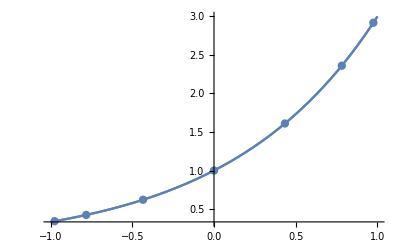

```mathematica
Show[Gr1,Gr2,Gr3]
```

# Задание 2.

```mathematica
g[x_]=Sin[9x];
```

```mathematica
n=1;
```

```mathematica
c=0;
d=3;
```

```mathematica
ϵ=10^-3;
```

```mathematica
M:=Maximize[{Abs[D[g[x],{x,n+1}]],c≤x≤d},x][[1]]
```

```mathematica
While[(M(d-c)^(n+1))/((n+1)!2^(2n+1))>ϵ,n++]
```

```mathematica
Do[{Subscript[x, i]=(d-c)/2 Cos[(Pi(2i+1))/(2(n+1))]+(c+d)/2,Subscript[g, i]=g[Subscript[x, i]]},{i,0,n}]
```

```mathematica
Tb2=Table[{Subscript[x, i],Subscript[g, i]},{i,0,n}]//N
```

{{2.9965,0.965095},{2.96863,0.999901},{2.91339,0.885599},{2.83183,0.34638},{2.72545,-0.567649},{2.59625,-0.98092},{2.44663,-0.0285348},{2.27938,0.995582},{2.0976,0.0288548},{1.9047,-0.990698},{1.70425,0.361348},{1.5,0.803784},{1.29575,-0.786191},{1.0953,-0.419565},{0.902398,0.964407},{0.720624,0.201052},{0.553368,-0.964323},{0.403746,-0.472497},{0.274545,0.621524},{0.168172,0.998362},{0.0866086,0.702908},{0.0313739,0.278628},{0.00349685,0.0314664}}

```mathematica
Do[Subscript[l, k][x_]=(∏_(i=0)^(k-1) (x-Subscript[x, i])/(Subscript[x, k]-Subscript[x, i]))(∏_(i=k+1)^n (x-Subscript[x, i])/(Subscript[x, k]-Subscript[x, i])),{k,0,n}];
H[x_]=∑_(k=0)^n Subscript[l, k][x] Subscript[f, k] //Expand//N
```

$Aborted

```mathematica
Gr1=Plot[g[x],{x,c,d}];
```

```mathematica
Gr2 = ListPlot[Tb2,PlotStyle->{PointSize[0.02]}];
```

```mathematica
Gr3=Plot[H[x],{x,c,d}];
```

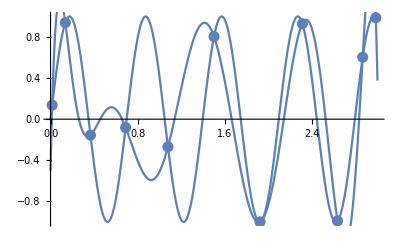

```mathematica
Show[Gr1,Gr2,Gr3]
```

# Задание 3.

```mathematica
ff[x_]=E^x
```

ⅇ^x

```mathematica
Subscript[x, 0]=0;
Subscript[x, 1]=0.1;
Subscript[x, 2]=0.2;
```

```mathematica
n=2;
```

```mathematica
t1=0.05;
```

```mathematica
t2=0.15;
```

```mathematica
ω[x_]=∏_(i=0)^n (x-Subscript[x, i])
```

(-0.2+x) (-0.1+x) x

```mathematica
M=Maximize[{Abs[D[ff[x],{x,n+1}]],0≤x≤0.2},x][[1]]//N
```

1.2214

```mathematica
R=M/((n+1)!)*Abs[ω[t1]]
```

0.0000763377

```mathematica
R=M/((n+1)!)*Abs[ω[t2]]
```

0.0000763377

# Задание 4.

```mathematica
fff[x_]=Cos[x];
n=5;
a=0;
b=1;
```

```mathematica
M=Maximize[{Abs[D[fff[x],{x,n+1}]],a≤x≤b},x][[1]]//N
```

1.

```mathematica
R=(M(b-a)^(n+1))/((n+1)!2^(2n+1))//N
```

6.78168×10^-7